```mathematica
Z[θ_,n_]:= (1-θ^n)/(1-θ)
```

```mathematica
g[θ_,n_]:=If[θ !=1, -(θ*Derivative[1,0][Z][θ,n]/Z[θ,n])^2+1/Z[θ,n]*(θ^2*Derivative[2,0][Z][θ,n]+θ*Derivative[1,0][Z][θ,n]),1/12 *(n^2-1)];
```

```mathematica
g[θ,n]//FullSimplify
```

Piecewise[{{1/12 (-1+n^2), θ==1}, {θ/(-1+θ)^2-(n^2 θ^n)/((-1+θ^n)^2), True}}]

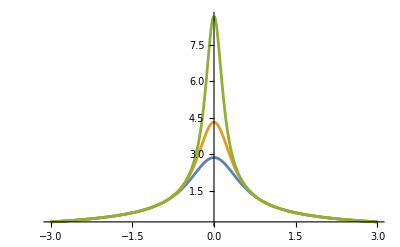

```mathematica
Plot[{Sqrt[g[Exp[-λ], 10]],Sqrt[g[Exp[-λ],15]],Sqrt[g[Exp[-λ],30]]},{λ, -3,3},PlotRange->All]
```

```mathematica
geodesicLengths = Table[{n,NIntegrate[Sqrt[g[Exp[-λ], n]],{λ,-3,3},WorkingPrecision->100]},{n,5,50}];
```

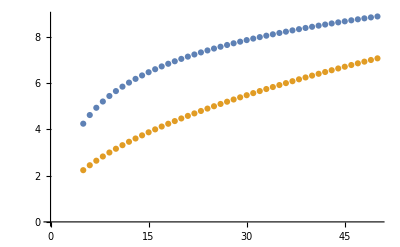

```mathematica
ListPlot[{geodesicLengths, Table[{n,Sqrt[n]},{n,5,50}]}]
```

```mathematica
Energies = Table[{n,6*NIntegrate[g[Exp[-λ], n],{λ,-3,3},WorkingPrecision->MachinePrecision]},{n,5,50}];
```

```mathematica
geodesicLengthsSquared = Table[{n, geodesicLengths[[n-4,2]]^2},{n,5,50}];
```

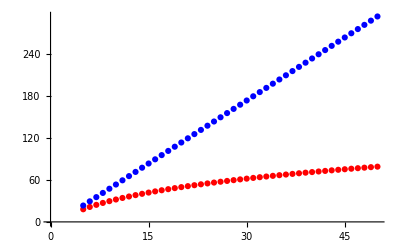

```mathematica
ListPlot[{geodesicLengthsSquared,Energies},PlotStyle->{Red,Blue}]
```

```mathematica
geodesicLengthsSquared
```

{{5,18.0282},{6,21.3458},{7,24.346},{8,27.0912},{9,29.6264},{10,31.9851},{11,34.1931},{12,36.2708},{13,38.2344},{14,40.0972},{15,41.8703},{16,43.5628},{17,45.1826},{18,46.7364},{19,48.23},{20,49.6683},{21,51.0558},{22,52.3962},{23,53.6932},{24,54.9496},{25,56.1682},{26,57.3515},{27,58.5017},{28,59.6208},{29,60.7106},{30,61.7727},{31,62.8087},{32,63.82},{33,64.8078},{34,65.7733},{35,66.7177},{36,67.6418},{37,68.5467},{38,69.4332},{39,70.3021},{40,71.1543},{41,71.9902},{42,72.8108},{43,73.6165},{44,74.4079},{45,75.1856},{46,75.9501},{47,76.702},{48,77.4415},{49,78.1693},{50,78.8856}}

```mathematica
Limit[g[θ,n],θ->1]
```

1/12 (-1+n^2)

```mathematica
g2[x_,n_]:= x/(-1+x)^2-(n^2 x^n)/((-1+x^n)^2);
```

```mathematica
NIntegrate[Sqrt[g2[Exp[-λ],10]],{λ,-3,3}]
```

5.65554

```mathematica
5.65^2/(6*10)
```

0.532042

```mathematica
g5 = Table[N[Sqrt[g[Exp[-3+6*i/600],5]]],{i,0,600}];
```

```mathematica
g15 = Table[N[Sqrt[g[Exp[-3+6*i/600],15]]],{i,0,600}];
```

```mathematica
g30 = Table[N[Sqrt[g[Exp[-3+6*i/600],30]]],{i,0,600}];
```

```mathematica
Export["Documents/NonGitCode/ComputationalEntropy/g5.csv", g5]
```

Documents/NonGitCode/ComputationalEntropy/g5.csv

```mathematica
Export["Documents/NonGitCode/ComputationalEntropy/g15.csv", g15]
```

Documents/NonGitCode/ComputationalEntropy/g15.csv

```mathematica
Export["Documents/NonGitCode/ComputationalEntropy/g30.csv", g30]
```

Documents/NonGitCode/ComputationalEntropy/g30.csv

```mathematica
f[x_,n_]:= Log[(1-Exp[-n*x])/(1-Exp[-x])];
```

```mathematica
Derivative[2,0][f][x,n]//FullSimplify
```

(ⅇ^x+ⅇ^(x+2 n x)-ⅇ^(n x) n^2-ⅇ^((2+n) x) n^2+2 ⅇ^(x+n x) (-1+n^2))/((-1+ⅇ^x)^2 (-1+ⅇ^(n x))^2)

```mathematica
p[x_,n_]:=Derivative[2,0][f][x,n]
```

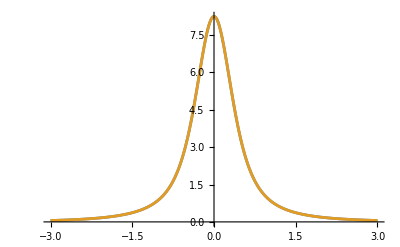

```mathematica
Plot[{p[x,10],g[Exp[-x],10]},{x,-3,3}]
```

```mathematica
f[x,n]//FullSimplify
```

Log[-(ⅇ^x (-1+(ⅇ^-x)^n))/(-1+ⅇ^x)]

```mathematica
f[x_,n_]
```

```mathematica
g[x,n]//FullSimplify
```

Piecewise[{{1/12 (-1+n^2), x==1}, {x/(-1+x)^2-(n^2 x^n)/((-1+x^n)^2), True}}]

```mathematica
p[Log[x],n]//FullSimplify
```

x/(-1+x)^2-(n^2 x^n)/((-1+x^n)^2)

```mathematica
Limit[p[x,n],x->0]
```

1/12 (-1+n^2)

```mathematica
f[Log[x],n]
```

Log[(1-x^-n)/(1-1/x)]